```mathematica
$Assumptions={S>0,s>0,σ>0,z>0,k>0,L>0,d>0,D0>0,v>0};
(*kp=-ⅈ s/2 + Sqrt[λ/d-s^2/4];
km=-ⅈ s/2 - Sqrt[λ/d-s^2/4];*)
kp=-ⅈ s/2 +k;
km=-ⅈ s/2 - k;
T=({{Exp[ⅈ kp*L/2], 0}, {0, Exp[ⅈ km*L/2]}});
U=({{1, 1}, {ⅈ*kp, ⅈ*km}});
M=({{1, -d*α}, {0, 1}});
S=({{1, -d*α}, {0, 1}})
MatrixForm[FullSimplify[T.Inverse[U].M.U.T/.α ->g*L/d]]
f[k_,s_]=Det[T.Inverse[U].M.U.T-IdentityMatrix[2]]
FullSimplify[f[z/L,S/(L)]/.α ->g*L/d]
```

(-(ⅈ ⅇ^(1/2 L (2 ⅈ k+s)) (4 k (2 ⅈ+g k L)+g L s^2))/(8 k) | -(ⅈ ⅇ^((L s)/2) g L (-2 ⅈ k+s)^2)/(8 k)
(ⅈ ⅇ^((L s)/2) g L (2 ⅈ k+s)^2)/(8 k) | (ⅇ^(1/2 L (-2 ⅈ k+s)) (8 k+4 ⅈ g k^2 L+ⅈ g L s^2))/(8 k))

1+ⅇ^(ⅈ L (-k-(ⅈ s)/2)+ⅈ L (k-(ⅈ s)/2))-ⅇ^(ⅈ L (-k-(ⅈ s)/2))-ⅇ^(ⅈ L (k-(ⅈ s)/2))-1/2 ⅈ d ⅇ^(ⅈ L (-k-(ⅈ s)/2)) k α+1/2 ⅈ d ⅇ^(ⅈ L (k-(ⅈ s)/2)) k α-(ⅈ d ⅇ^(ⅈ L (-k-(ⅈ s)/2)) s^2 α)/(8 k)+(ⅈ d ⅇ^(ⅈ L (k-(ⅈ s)/2)) s^2 α)/(8 k)

```mathematica
-(ⅇ^(S/2) (8 z Cos[z]-8 z Cosh[S/2]+g (S^2+4 z^2) Sin[z]))/(4 z)
```

```mathematica
MatrixForm[FullSimplify[T.M.T]]
```

(ⅇ^(1/2 L (2 ⅈ k+s)) | -d ⅇ^((L s)/2) α
0 | ⅇ^(1/2 L (-2 ⅈ k+s)))

```mathematica
Cos[z]+g (S^2/4+ z^2) Sin[z]/(2*z)/.z->Sqrt[λ-S^2/4]
```

Cos[√(-S^2/4+λ)]+(g λ Sin[√(-S^2/4+λ)])/(2 √(-S^2/4+λ))

```mathematica
NSolve[1+5000*S^2/8==Cosh[S/2],S]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[1+625 S^2==Cosh[S/2],S]

```mathematica
g=4160;FindRoot[1+g*S/2-Cosh[S/2],{S,100}]
```

{S→22.9316}

```mathematica
Manipulate[λ=x+ⅈ y;
Plot[ {Re[Cos[√(-S^2/4+λ)]+(g λ Sin[√(-S^2/4+λ)])/(2 √(-S^2/4+λ))]-Cosh[S/2],Im[Cos[√(-S^2/4+λ)]+(g λ Sin[√(-S^2/4+λ)])/(2 √(-S^2/4+λ))],Sqrt[1+(g*λ/(2 √(-S^2/4+λ)))^2]-Cosh[S/2]},{x,0,1000},GridLines->{{S^2/4},{}},PlotRange->{-5Cosh[S/2],5*Cosh[S/2]}],{g,0.,10^4},{S,0,200},{y,0,S^2}]
```

```mathematica
Solve[D[(g λ)/(2 √(-S^2/4+λ)),λ]==0,λ]
```

{{λ→S^2/2}}

```mathematica
(g S^2/2)/(2 √(-S^2/4+S^2/2))
```

(g √(S^2))/2

```mathematica
FullSimplify[Solve[Sqrt[1+(g*λ/(2 √(-S^2/4+λ)))^2]==Cosh[S/2],λ]]
```

{{λ→-(4-4 Cosh[S]+√((-4+4 Cosh[S])^2+8 g^2 (S^2-S^2 Cosh[S])))/(4 g^2)},{λ→(-4+4 Cosh[S]+√((-4+4 Cosh[S])^2+8 g^2 (S^2-S^2 Cosh[S])))/(4 g^2)}}

```mathematica
g=100;FindRoot[1+g*S/2-Cosh[S/2],{S,100}]
```

{S→14.5712}

```mathematica
Manipulate[z=x+ⅈ*y;

Plot[ {Re[Cos[z]+g (S^2/4+ z^2) Sin[z]/(2*z)]-Cosh[S/2],Im[Cos[z]+g (S^2/4+ z^2) Sin[z]/(2*z)],(5*π/4)*g*Cosh[y]*(1+S^2/(25π^2+4y^2))-Cosh[S/2](*Sqrt[1+(g (S^2/4+ x^2)/(2x))^2]*)},{x,0,50},GridLines->{{3π/2,5π/2},{}}],{g,0.,10^3.},{S,0,50},{y,0,S}]
```

```mathematica
Manipulate[z=x+ⅈ*y;

Plot[ {Im[Cos[z]+g (S^2/4+ z^2) Sin[z]/(2*z)]},{x,0,50},GridLines->{{3π/2,5π/2},{}},PlotRange->{-5,5}],{g,0.,10^3.},{S,0,50},{y,0,2*S}]
```

```mathematica
Series[Cosh[(S+Δ)/2],{Δ,0,1}]
```

Cosh[S/2]+1/2 Sinh[S/2] Δ+O[Δ]^2

```mathematica
g=100;s=15;x=5π/2;Manipulate[Plot[{Cosh[y],1+y^2/2,2/(g*x)*(x^2+y^2)/(x^2+y^2+s^2/4)*Cosh[s/2]},{y,0,1}],{s,10,20}]
```

```mathematica
N[5*π/2]
```

7.85398

```mathematica
Sin[5π/2]
```

1

```mathematica
Manipulate[Plot[{g*λ*Sin[Sqrt[s^2/4-λ]]/Sqrt[s^2/4-λ]+Cos[Sqrt[s^2/4-λ]],Cosh[s/2]},{λ,10*π}],{s,0,10},{g,0,10}]
```

Plot::pllim: Range specification {λ, 10\ π} is not of the form {x, xmin, xmax}.

Plot::pllim: Range specification {Parallel`Combine`Private`λ, 10\ π} is not of the form {x, xmin, xmax}.

```mathematica
Limit[(g λ Sin[√(-S^2/4+λ)])/(2 √(-S^2/4+λ)),λ->S^2/4]
```

(g S^2)/8

```mathematica
Solve[D[1+(g*λ/(2 √(-S^2/4+λ)))^2,λ]==0,λ]
```

{{λ→0},{λ→S^2/2}}

```mathematica
Sqrt[1+(g*λ/(2 √(-S^2/4+λ)))^2]/.λ->S^2/2
```

√(1+(g^2 S^2)/4)

```mathematica
g=10^7;FindRoot[Sqrt[1+(g*S/2)^2]-Cosh[S/2],{S,100}]
```

{S→39.5935}

```mathematica
S
```

S

```mathematica
S/.{S->11.673586006831915}
```

11.6736

```mathematica
Sg
```

Sg

```mathematica
S/.{S->11.673586006831915}
```

11.6736

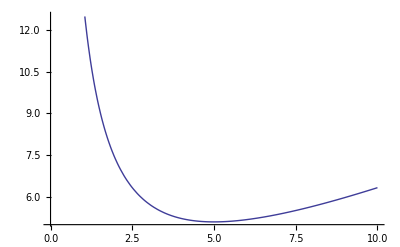

```mathematica
g=1;s=10;Plot[Sqrt[1+g^2*((k^2+(s/2)^2)/(2*k))^2],{k,0,s}]
```